```mathematica
(* create association between SP and their shate tolerance index: mmaybe obsolete *)
spID = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_all_data/all_clean_ID.csv"];

spID = Select[spID,( #[[1]] ≠ "Celtis" && #[[1]] ≠ "balsamea") &] ;
ID = spID[[All,2]]//Union;
SP =spID[[All,1]]//Union;
```

```mathematica
as = Directive[14,Black,FontFamily->"Helvetica"];
is = 300;
sf = {"Reverse",Identity};
ls =Directive[Black, FontFamily->"Helvetica",16];

aA = Style["A) \n", LineSpacing->{0.3, 0},as];
aB = Style["B) \n", LineSpacing->{0.3, 0},as];
aC = Style["C) \n", LineSpacing->{0.3, 0},as];
aD = Style["D) \n", LineSpacing->{0.3, 0},as];
aE = Style["E) \n", LineSpacing->{0.3, 0},as];
aF = Style["F) \n", LineSpacing->{0.3, 0},as];
aG = Style["G) \n", LineSpacing->{0.3, 0},as];
aH = Style["H) \n", LineSpacing->{0.3, 0},as];
aI = Style["I) \n", LineSpacing->{0.3, 0},as];

On[Assert];

NewSeparateAC[data_,thresh_:0.5,Rand_:True]:= Module[{result,age,post,mean,pp,val,m1,m2},
age = data[[1]];
post = data[[2]];
mean = data[[3]];
Assert[Length@age ==Length@post == Length@mean];
pp =Unitize[post,thresh];

If[pp[[1]] == 1 && mean[[1]] < mean[[2]], pp[[1]] = -1];
Do[
val = pp[[i]];
If[val == 1,
m1  = mean[[i]];
m2 = mean[[i+1]];
If[m1 <m2, pp[[i]] = -1];
];
,{i,2,Length@age -1}];
(*If[pp[[-1]] == 1 && mean[[-2]] < mean[[-1]], pp[[1]] = -1];
*)
Do[
If[pp[[i-1]] == 0 && pp[[i+1]] == (-1 pp[[i]]) && pp[[i+2]]==0,
pp[[i]]= 0; pp[[i+1]]=0];
,{i,2,Length@age-2}];

result = Transpose[{age,pp}];
result = Select[result,#[[2]] == 1 || #[[2]] == -1&];
result
];

(* finds the successive duplicates, averages the frequency and delete the second duplicate *)
AverageDeleteDuplicates[dat_]:=Module[{temp,age,pos, meanval, result},
temp = dat;

age = Select[Tally[temp[[All,1]]],#[[2]] >1&][[All,1]];
Do[
pos = Position[temp[[All,1]],age[[i]]]//Flatten;
Assert[Length@pos ==2 && pos[[2]] == (pos[[1]] +1)];
meanval =Mean[temp[[pos]]];
Table[temp[[pos[[j]]]] = meanval,{j, Length@pos}];
temp =Delete[temp, pos[[2]]]; 
,{i, Length@age}];
result = temp;
result];
```

## Data cleaning and compilation

### Cleaning Pinus

```mathematica
(* list of all the Pinus subg. that was downloaded*)dpin = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/all_selected_pinus.csv"];

(* partition the 2 subtypes of pin NPP for Pinus pinus and NPS for Pinus strobus*) 
(* these names where obtained after preliminary analyses (see above) using allPinus list and collecting the final outpout *)
pinus = Union[dpin[[All,1]]]//Sort;
pp =  {"Pinus banksiana","Pinus banksiana-type","Pinus resinosa-type","Pinus subg. Pinus"};
ps = {"Pinus strobus", "Pinus subg.Strobus", "Pinus subg.Strobus undiff.", "Pinus det.P.strobus"};
npp = Select[dpin, MemberQ[pp,#[[1]]]==True&];
nps = Select[dpin, MemberQ[ps,#[[1]]]==True&];

NPP = GroupBy[npp,Last];
NPS = GroupBy[nps,Last];
```

```mathematica
(* create and export time series with the 2-subtypes *)
ALLDAT = {NPP,NPS};
nmout = {"PinusPinus_","PinusStrobus_"};
Do[
DAT = ALLDAT[[i]];
KZ= Keys[DAT];
Do[
names = DAT[kz];
ln = Length[names];
nm  = names[[1]];
nmin = "/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/"<>ToString@nm[[1]]<>"_"<>ToString@kz<>".csv";
dat = Import[nmin][[2;;]] /. "NA" -> 0.;

If[ln >1,
Do[
nm  = names[[i]];
mored = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/"<>ToString@nm[[1]]<>"_"<>ToString@kz<>".csv"][[2;;]]/. "NA" -> 0.;
(* add the proportion *)
dat[[All,2]]+= mored[[All,2]];
,{i,2,ln}];
];
(*removes all NA*)
outd = Select[dat,NumericQ[#[[2]]]==True&];
PrependTo[outd,{"age", StringDrop[nmout[[i]],-1]}];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/"<>nmout[[i]]<>ToString@kz<>".csv",outd]
,{kz,KZ}];
,{i,2}];
```

#### Compile site_info for both Pinus

```mathematica
infoPP = {"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus banksiana_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus banksiana-type_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus subg. Pinus_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus resinosa-type_site_info.csv"};

infoPS = {"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus det. P. strobus_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus strobus_site_info.csv",
"/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus subg. Strobus_site_info.csv",
"//Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/Pinus/Pinus subg. Strobus undiff._site_info.csv"};
```

```mathematica
dP =Flatten[ Import[#][[2;;,2;;]] &/@infoPP ,1];
dS =Flatten[ Import[#][[2;;,2;;]] &/@infoPS ,1];

dPP = DeleteDuplicates[dP];
dPS = DeleteDuplicates[dS];

rownP = Range[Length@dPP];
rownS = Range[Length@dPS];

ndPP =dPP//Transpose;
ndPS =dPS//Transpose;

oPP = PrependTo[ndPP,rownP]//Transpose;
oPS = PrependTo[ndPS,rownS]//Transpose;

coln = {"","site.name", "dataset.id", "site.id", "lat", "long"};
PrependTo[oPP, coln];
PrependTo[oPS, coln];

Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/PinusPinus_site_info.csv",oPP];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/PinusStrobus_site_info.csv",oPS];
```

### Clean raw data: replace age-model, trim, length, number of zero, average and delete duplicates

```mathematica
AMlist  = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_ID_age-model.csv"][[All,1]];
SpSite = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/all_rawsp.csv"];

(*var05 is extracted from Nieto-Lugildeetal_2015_GEB, Appendix 1*)
var05 = AssociationThread[Union[SpSite[[All,1]]] -> {2.25,1.2,0.08,0.95,4.28,4.28,0.12,0.11,0.97,1.34}/100]
```

<|Alnus→0.0225,Fagus→0.012,Juglans→0.0008,Picea→0.0095,PinusPinus→0.0428,PinusStrobus→0.0428,Platanus→0.0012,Tilia→0.0011,Tsuga→0.0097,Ulmus→0.0134|>

```mathematica
allID= Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_site_ID.csv"]//Flatten;
```

```mathematica
agemodel = {};
Do[
amdata = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/age-model/Bchron_summary_"<>ToString@im<>".csv"][[2;;,4]];
AppendTo[agemodel,amdata];
,{im, AMlist}]
```

```mathematica
(* associates each age model with the site ID *)
assocAM  = AssociationThread[AMlist,agemodel];
```

```mathematica
(* Criteria age 8000-1000, range = 3000, the zero should be less than a third, length ≥ 20, frequency ≥ 1% *)
On[Assert];
DUPLID = {};SELID = {};
Do[
name = ss[[1]];
id = ss[[2]];
(*Print[name, "_",id];*)
(* assumes that the NA are 0 *)
dat = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/"<>name<>"_"<>ToString@id<>".csv"][[2;;]]/."NA"-> 0.;

(* substitute old to the new age models *)
If[MemberQ[AMlist, id]==True,
age = assocAM[id];
Assert[Length@dat == Length@age]; (* check in the code *)
dat[[All,1]] = age;
];

(* select age between 8000 and 1000 YBP *)
ndat = Select[dat, (#[[1]] ≤  8000 && #[[1]] ≥ 1000)& ];

(* compute the number of rows (length) of the data and sort from older to younger *)
len = Length[ndat];If[len == 0, Goto["here"]];
ndat = Sort[ndat, (#1[[1]] ≥ #2[[1]])&];

old = ndat[[1,1]]; (* select the oldest age*)
yng = ndat[[-1,1]]; (* select the youngest age*)
rng = old - yng; (* compute the range of the data*)
If[rng ≤ 0 && Length@ndat > 1, Print[name,"_",id,"_",rng]]; (* check in the code *)
(*Assert[rng >0.];*)

nzero = Count[ndat[[All,2]],0.]; (* count the number of zero*)
maxf = Max[ndat[[All,2]]]; (* extract the maximum relative abundance *)

If[len ≥ 20 && rng ≥ 3500 && maxf≥var05[name] && nzero/len ≤  1/3. && MemberQ[allID,id]==True , 
If[DuplicateFreeQ[ndat[[All,1]]]== False, AppendTo[DUPLID, id]; ndat = AverageDeleteDuplicates[ndat]];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>name<>"_"<>ToString@id<>".csv",ndat];
AppendTo[SELID ,ss];
];

Label["here"]
,{ss,SpSite }];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_clean_ID.csv",SELID];
```

The timeline: download all sites, select good site, export good site, new selection due to bad age-model, and add the new selection to the criteria for selecting good site (hence the MemberQ above)

This is post analyses.

Initially, there was a long list of initial pre-selected sites that was displayed in a table. Allison removed sites that had bad age-model and provided the final list of sites. The code below just double check that we are not missing sites.

```mathematica
(* SELID removing MemberQ*) 
ca1 =SELID[[All,2]]//Union
```

{7,232,238,275,375,516,532,538,672,677,679,684,834,878,971,973,1002,1105,1520,1571,1590,1615,1698,1768,1786,1820,1824,1888,1981,2023,2065,2270,2292,2332,2341,2959,2961,3031,3058,3487,3558,3781,13029,13032,13047,13051,14410,14614,15032,15035,15138,15140,15207,15209,15302,15309,15403,15660,15682,15732,15819,15866,15904,15909,16231,17387,17396,17404,17689,18110,19834,19937,20194,20397,21389}

```mathematica
Length@%
```

75

```mathematica
(* final list from Table S2 *) ca2 = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_site_ID.csv"]//Flatten
```

{7,238,275,375,516,532,672,677,679,684,878,971,973,1002,1105,1520,1571,1590,1615,1698,1768,1786,1820,1824,1888,1981,2023,2065,2270,2292,2332,2959,2961,3031,3058,3487,3558,3781,13029,13032,13047,13051,14410,14614,15032,15035,15138,15140,15207,15302,15309,15403,15660,15682,15732,15819,15866,15904,15909,16231,17396,17404,17689,17387,18110,19834,19937,20194,20397,21389}

```mathematica
Length@%
```

70

```mathematica
Flatten[{ca1,ca2}]//Tally
```

{{7,2},{232,1},{238,2},{275,2},{375,2},{516,2},{532,2},{538,1},{672,2},{677,2},{679,2},{684,2},{834,1},{878,2},{971,2},{973,2},{1002,2},{1105,2},{1520,2},{1571,2},{1590,2},{1615,2},{1698,2},{1768,2},{1786,2},{1820,2},{1824,2},{1888,2},{1981,2},{2023,2},{2065,2},{2270,2},{2292,2},{2332,2},{2341,1},{2959,2},{2961,2},{3031,2},{3058,2},{3487,2},{3558,2},{3781,2},{13029,2},{13032,2},{13047,2},{13051,2},{14410,2},{14614,2},{15032,2},{15035,2},{15138,2},{15140,2},{15207,2},{15209,1},{15302,2},{15309,2},{15403,2},{15660,2},{15682,2},{15732,2},{15819,2},{15866,2},{15904,2},{15909,2},{16231,2},{17387,2},{17396,2},{17404,2},{17689,2},{18110,2},{19834,2},{19937,2},{20194,2},{20397,2},{21389,2}}

```mathematica
DUPLID//DeleteDuplicates (* site that have at least two points with the same age *)
```

{13029,15138,19834,14410}

### Compile site info: Dataset: DA: occurrences and number of Ax

```mathematica
(* import all pair taxaname datasetID*)
spID = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_clean_ID.csv"];

(* obain all unique taxaname and datasetID *)
ID = spID[[All,2]]//Union;
SP =spID[[All,1]]//Union;

(* create column ID for each taxa and types of abrupt change *)
SPAC =StringJoin[#,"_AC"] & /@ SP;
SPAI =StringJoin[#,"_AI"] & /@ SP;
SPAD =StringJoin[#,"_AD"] & /@ SP;

(* store all sites where the taxa is present *)
allD = {};
Do[
dat = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/raw_allsp_data/"<>sp<>"_site_info.csv"][[2;;,2;;]];
allD = Join[allD,dat];
,{sp, SP}];
allD =  DeleteDuplicates@allD;(* all the sites where any taxa is present *)

(* SP tells whether the taxa is present or not, num_Ax is the number of abrupt change *)
col = {"datasetID","lon","lat", "name","num_points","mean_resol","old_year","range", "num_sp","num_AD","num_AI","num_AC",SP,SPAC,SPAI,SPAD}//Flatten;

(* store all the info in this table*)
data = ConstantArray[Null,{Length@ID, Length@col}];
(* this loop essentially go over all datasetID, collect site info (e.g. range, lat, long etc. ), find which species are present, and fill the number of AC for each species*)
Do[
id = ID[[i]]; (* why using ID here instead of the second column in allD? It should be the same, no because ID from all_clean_ID is cleaner *)

sid = Select[allD,#[[2]] == id &][[1]];
name = sid[[1]];
lat = sid[[4]];
lon = sid[[5]];

(* all species that belong to occurs in that site *)
allSP = Select[spID, #[[2]]==id &];
ns = Length@allSP;

sp = allSP[[1,1]]; (*use the first species to get the age *)
temp  = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>sp<>"_"<>ToString@id<>".csv"];

age = temp[[All,1]];
np = age //Length; (* data length *)
mr =  age//Differences//Abs//Mean //N; (* mean duration between successive age *)
oy = Max@age;
rg = oy - Min@age;

nD  = nI = nC = 0;
(*Loop over taxa*)
Do[
pos = Position[col, spp]//Flatten; 
data[[i,pos]] = 1; (* the taxa is present *)

ed = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_"<>ToString@id<>".csv"];em = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_pm_"<>ToString@id<>".csv"];ep= Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_pp_"<>ToString@id<>".csv"];

rac = NewSeparateAC[{ep[[All,1]],ep[[All,2]],em[[All,2]]},0.5,False];
ac = rac[[All,2]];
aci = Count[ac,-1];
acd = Count[ac,1];

nD += acd;
nI += aci;
nC += acd + aci;

pos2 = Position[col, spp<>"_AC"]//Flatten;
data[[i,pos2]] = acd +aci;

posi = Position[col, spp<>"_AI"]//Flatten;
data[[i,posi]] = aci;

posd = Position[col, spp<>"_AD"]//Flatten;
data[[i,posd]] = acd;

,{spp, allSP[[All,1]]}];

vect = {ToString@id,lon,lat,name, np,mr,oy,rg,ns, nD,nI,nC};
data[[i,;;12]] = vect;

,{i, Length@ID}];
```

```mathematica
DA = Dataset[data /. Null->0][All,AssociationThread[col,Range[Length[col]]]];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/site_info.m",DA];
```

```mathematica
(* Export as a csv *)
oda1 = DA//Normal//Values;
oda = PrependTo[oda1,col];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/site_info.csv",oda];
```

```mathematica
sites = DA[All,1;;4]//Normal//Values;
PrependTo[sites, {"datasetID", "long","lat","name"}];
```

```mathematica
(*this is not longer needed, it was used to provide the data to Allison for the age-model *)Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_sites.csv",sites]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_sites.csv

```mathematica
(* In case there is need to re-import the data *)
DA = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/site_info.m"];
```

### Compile species info: Dataset: DS: timing of A_

```mathematica
ASSOC = {};
(* Loop over species *)
Do[
pASS = {};
sID = Select[spID, #[[1]] ==spp&][[All,2]];
Do[ (* for each site *)

ed = Import["//Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_"<>ToString@id<>".csv"];em = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_pm_"<>ToString@id<>".csv"];ep= Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_pp_"<>ToString@id<>".csv"];

sac = NewSeparateAC[{ep[[All,1]],ep[[All,2]],em[[All,2]]},0.5, False];

ti = Select[sac,(#[[2]]==-1 &)][[All,1]];
td = Select[sac,(#[[2]]==1 &)][[All,1]];
tc = Join[ti,td];
If[Length@tc >0,
ass = {"AC" ->tc};
If[Length@td>0, assd="AD"->td; PrependTo[ass,assd]];
If[Length@ti>0,assi = "AI"->ti; PrependTo[ass,assi]];
 assoc= ToString@id -> Association[ass];
AppendTo[pASS, assoc];
];
,{id,sID}];
ast = Association[spp ->  Association[pASS]];
AppendTo[ASSOC ,ast];
,{spp, SP}];

DS = Dataset[Association[ASSOC]];
```

```mathematica
(*Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/AC_info.json",DS,"JSON"];*)
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/AC_info.m",DS];
```

```mathematica
(* Export the data into a long form stuff *)
RES = {};
K1 = DS//Keys;
Do[
K2 = DS[K1[i1]]//Keys;
Do[
K3 = DS[K1[i1],K2[i2]]//Keys;
Do[
vv= DS[K1[i1],K2[i2], K3[i3]]//Normal;
val  = Table[{K1[i1],K2[i2], K3[i3],vv[[j]]},{j,Length@vv}];
AppendTo[RES,val];
,{i3,Length@K3}];
,{i2,Length@K2}];
,{i1, Length@K1}];
```

```mathematica
pout = Partition[RES//Flatten,4];
out = PrependTo[pout,{"taxa", "datasetID","Type of abrupt change","Time"}];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/AC_info.csv",out];
```

```mathematica
DS = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/AC_info.m"];
```

## Plot wrt to time for each taxa, sites,

```mathematica
(* manually selected ticks for the y-axis*)
tx = {Automatic,{{0,"0.0"},{0.0005,"0.5"},{0.001,"1.0"},{0.0015,"1.5"},{0.003,"2.0"}}};
spID = Import["//Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_clean_ID.csv"];

ID = spID[[All,2]]//Union;
SP =spID[[All,1]]//Union;


COLSP = {Yellow, Pink, Orange, Red,Brown,Green,Cyan,Blue,Gray,Black};

colSP = AssociationThread[SP,COLSP];

pr3a = {{1200,8500},{0,All}};
pr3aa= {{1200,8500},{0,1.0}};
pr3b =  {{1200,8500},{0,0.001}};

ip = {{30,10},{16,10}};
ip2 = {{24,10},{16,10}};
```

### Plot AC per species, Fig S3

```mathematica
ALLFIG = {};
Do[
(* import empirical data *)
DDA = {};
sID = Select[spID, #[[1]] ==spp&][[All,2]];
Do[ (* for each site *)
ed = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_"<>ToString@id<>".csv"];
AppendTo[DDA,ed];
,{id,sID}];

nn = Length@sID;
eg =  Text[Framed[Style["N = "<> ToString@nn,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
lb = {"Relative abundance", "Years Before Present"}; 
f5=Labeled[ListLinePlot[DDA,Epilog->eg,PlotRange->pr3a,AxesOrigin->{8500,0},PlotStyle->Directive[Gray,AbsoluteThickness[0.6]],AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,LabelStyle->ls, PlotLabel->Style[spp,16,Italic,FontFamily->"Helvetica"],ImagePadding->ip],lb,{Left,Bottom},RotateLabel->True,LabelStyle->ls];

(* separates the abrupt increase and decrease from the empirical data *)
empi = DS[spp,All,"AI"]//DeleteMissing//Normal //Values//Flatten;
empd = DS[spp,All,"AD"]//DeleteMissing//Normal //Values//Flatten;

gd  = {empd,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[empd]]}//Transpose;
gi  = {empi,ConstantArray[Directive[Gray,AbsoluteThickness[1],Opacity[1]],Length[empi]]}//Transpose;

(* compute the coefficient of variation *)
edi = Differences[Sort@empi] ;
edd = Differences[Sort@empd] ;
If[Length@edi>2,
cvi1 = StandardDeviation@edi/Mean@edi,
"NA"
];
 
If[Length@edd>2,
cvd1 = StandardDeviation@edd/Mean@edd,
"NA"];

(* if there are not many sites, just plot the bars without the smoothing, might change the length to 3 or 4 *)
lb2 = {"Density", "Years Before Present"};
(* for abrupt decreases *)
If[Length@empd > 2,
eg =  Text[Framed[Style["N = "<> ToString@Length@empd<>"\nCV="<>ToString@Round[cvd1,0.02],12,FontFamily->"Helvetica"],Background->White],Scaled[{0.85,.88}]];
f5C= SmoothHistogram[empd,{200,"Gaussian"},
Epilog->eg,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.0017}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gd,None},LabelStyle->ls,PlotLabel->"Abrupt decreases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2],
eg = Text[Framed[Style["N = "<> ToString@Length@empd<>"\nCV= NA",12,FontFamily->"Helvetica"],Background->White],Scaled[{0.85,0.88}]];
f5C = ListLinePlot[{empd,1}//Flatten,Epilog->eg,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],PlotRange-> {{800,8500},{0,0.0017}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gd,None},LabelStyle->ls,PlotLabel->"Abrupt decreases",ImageSize->is,Ticks->tx,ImagePadding->ip2]
];
f5C = Labeled[f5C, lb2,{Left,Bottom},RotateLabel->True,LabelStyle->ls];

(* for abrupt increases *)
If[Length@empi >2,
eg = Text[Framed[Style["N = "<> ToString@Length@empi<>"\nCV="<>ToString@Round[cvi1,0.02],12,FontFamily->"Helvetica"],Background->White],Scaled[{0.85,.88}]];
f5E = SmoothHistogram[empi,{200,"Gaussian"},
Epilog->eg,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.0017}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gi,None},LabelStyle->ls,PlotLabel-> "Abrupt increases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2],
eg = Text[Framed[Style["N = "<> ToString@Length@empi<>"\nCV= NA",12,FontFamily->"Helvetica"],Background->White],Scaled[{0.85,.88}]];
f5E = ListLinePlot[{empi,1}//Flatten,Epilog->eg, AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],PlotRange-> {{800,8500},{0,0.0017}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gi,None},LabelStyle->ls,PlotLabel->"Abrupt increases",ImageSize->is,Ticks->tx,ImagePadding->ip2]
];
f5E= Labeled[f5E, lb2,{Left,Bottom},RotateLabel->True,LabelStyle->ls];

FF = {f5,f5C,f5E};
AppendTo[ALLFIG, FF];
,{spp, SP}];
```

```mathematica
aF = Grid[ALLFIG,Spacings->{Automatic, 2}];
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/figS3.pdf",aF]
```

### Plot AC per site

```mathematica
spID = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/all_clean_ID.csv"];

ID = spID[[All,2]]//Union;

ALLFIG = {};
Do[
(* import empirical data *)
DDA = SAC  ={};
sSP = Select[spID, #[[2]] ==id&][[All,1]];

col = colSP[#]&/@ sSP;

gd = gi = empd = empi =  {};
Do[ 
ed = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>spp<>"_"<>ToString@id<>".csv"];
AppendTo[DDA,ed];

dd = DS[spp, ToString@id,"AD"]//Normal;
fdd = Table[{dd[[i]],Directive[colSP[spp],AbsoluteThickness[2],Opacity[1]]},{i,Length@dd}];
gd = Join[gd,fdd];

ii = DS[spp, ToString@id,"AI"]//Normal;
fii = Table[{ii[[i]],Directive[colSP[spp],AbsoluteThickness[2],Opacity[1]]},{i,Length@ii}];
gi = Join[gi,fii];

,{spp,sSP}];

gd = Select[gd, NumericQ[#[[1]]]==True &];
gi = Select[gi, NumericQ[#[[1]]]==True &];

(* apparently this is needed so the plot argument is not empty *)
empd =gd[[All,1]];
empi =gi[[All,1]];

f5=ListLinePlot[DDA,PlotRange->pr3a,AxesOrigin->{8500,0},PlotStyle->col,AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,LabelStyle->ls, PlotLabel->ToString[id]<>"_"<>ToString[Length@sSP]];

f5C = ListLinePlot[empd,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gd,None},LabelStyle->ls,PlotLabel->"Abrupt decreases_"<>ToString[Length@empd],ImageSize->is,Ticks->tx];

f5E = ListLinePlot[empi,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gi,None},LabelStyle->ls,PlotLabel->"Abrupt increases_"<>ToString[Length@empi],ImageSize->is,Ticks->tx];

lg2 = LineLegend[col,sSP];
FF = {lg2,f5,f5C,f5E};
AppendTo[ALLFIG, FF];
,{id, ID}];
```

```mathematica
aF = Grid[ALLFIG];
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/figs_AC_all_site.pdf",aF]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/figs_AC_all_site.pdf

### Plot pre species per site

```mathematica
lgS = PointLegend[{Gray,Black,Blue,Red},{"Original data","Fitted with bcp","Abrupt increases","Abrupt decreases"},LegendMarkers->{{Graphics[{Black,AbsoluteThickness[0.5],Line[{{1,0},{20,0}}]}],20},{"—",20},{"|",20},{"|",20}},LabelStyle->ls]
```

```mathematica
(* import data for all empirical data (time-series, fitted mean, and posterior probability *)
IP = {{30,10},{20,20}};
SI = SD  = {};
Do[

FIG = ACI = ACD ={};
ID = DA[Select[#[sp]==1&],"datasetID"]//Normal;
Do[

ed = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>sp<>"_"<>ToString@id<>".csv"];
em = Import["/Users/gola/Box Sync/projects/ACES_paleo_lottery/data/clean_allsp_data/"<>sp<>"_pm_"<>ToString@id<>".csv"];

dd = DS[sp,ToString@id,"AD"];

empi= DS[sp,ToString@id,"AI"]//Normal ;
empd= DS[sp,ToString@id,"AD"]//Normal;

gd  = Table[{empd[[i]],Directive[Red,AbsoluteThickness[1],Opacity[1]]},{i,Length[empd]}];
gi  = Table[{empi[[i]],Directive[Blue,AbsoluteThickness[1],Opacity[1]]},{i,Length[empi]}];

gd = Select[gd, NumericQ[#[[1]]]==True &];
gi = Select[gi, NumericQ[#[[1]]]==True &];

gdl = {Join[gd,gi],None};

fig = ListLinePlot[{ed,em},PlotRange->{All,{0,Max[ed[[All,2]]]}}, PlotStyle-> {{Black,Thin},Black},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{Max[ed[[All,1]]],0},GridLines->gdl,FrameStyle->Directive[12,Black,FontFamily->"Arial"],
PlotRangePadding->None,Frame->True,PlotLabel->"Dataset ID: "<>ToString@id, LabelStyle->Directive[12,Black,FontFamily->"Arial"],ImageSize->250,ImagePadding->IP];
AppendTo[FIG,fig];

,{id,ID}];
AppendTo[SI,ACI];
AppendTo[SD, ACD];

PrependTo[FIG,lgS];

FF = Partition[FIG,4];
out =Labeled[Grid[FF],{"Years Before Present","Frequency","Figure S3_" <> sp},{Bottom,Left,Top},RotateLabel->True,LabelStyle->Directive[16,Black,FontFamily->"Arial"]];

Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/figS3_"<>sp<>".pdf",out];

,{sp,SP}]
```

## Plot Map

```mathematica
(*IT = Range[1000,11700,2000]*)
```

{1000,3000,5000,7000,9000,11000}

```mathematica
(*IT = Range[1000,8000,1300]*)
```

{1000,2300,3600,4900,6200,7500}

```mathematica
(*(* symbol used for figure 3*)
IT = Range[1000,11700,2000];
StyleSelector[age_]:= Which[
age ≤ IT[[2]],Graphics[{EdgeForm[{AbsoluteThickness[2], Black}],Black,Disk[{0,0},0.1]}],
IT[[2]]< age ≤ IT[[3]],Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[0.2]}],GrayLevel[0.2],Disk[{0,0},0.1]}],
IT[[3]]< age ≤ IT[[4]],Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[0.5]}],GrayLevel[0.5],Disk[{0,0},0.1]}],
IT[[4]]< age ≤ IT[[5]],Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[0.8]}],GrayLevel[0.8],Disk[{0,0},0.1]}],
IT[[5]]< age ,Graphics[{EdgeForm[{AbsoluteThickness[1],Gray}],White,Disk[{0,0},0.1]}]
 ];

st =Style[#,12,Black, FontFamily->"Arial"] &/@ { "11700",  "9000", "7000", "5000", "3000","1000"};

XY = Partition[Flatten[Table[{x,y},{x, Subdivide[39,48.,3]},{y,Subdivide[-88,-62.,7]}]],2];*)
```

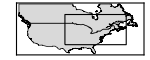

```mathematica
(*(* uncomment if an inset needs to be created *)f3inset =GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[LightGray]],Polygon[ LinguisticAssistant]},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[LightGray]],Polygon[ LinguisticAssistant]},EdgeForm[{Thick,Black}],FaceForm[],Rectangle[{-100,35},{-60,65}]}, GeoRange->{{25,60},{-130,-50}},ImageSize->150,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White], AspectRatio->1/2.5,GeoProjection->"Mercator"]
*)
```

### General map

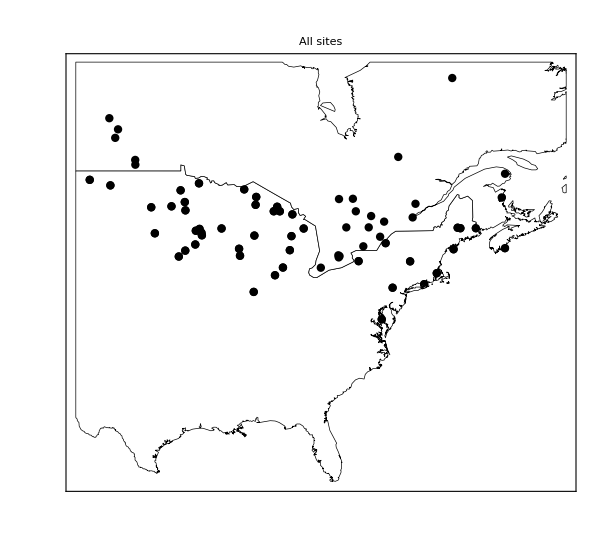

```mathematica
pt = Graphics[{EdgeForm[{AbsoluteThickness[2], Black}],Black,Disk[{0,0},0.1]}];
SeedRandom[1];
allp = Table[{GeoMarker[RandomReal[{-0.25,0.25},2] + Values[Normal[DA[i,{"lat","lon"}]]],pt,"Scale"-> 0.6]},{i,Length@DA}];

gr ={{25.,55.5},{-105.,-59.}};
ffA=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->600,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,LabelStyle->Directive[Black,12,FontFamily->"Arial"] ,PlotLabel->"All sites"]
```

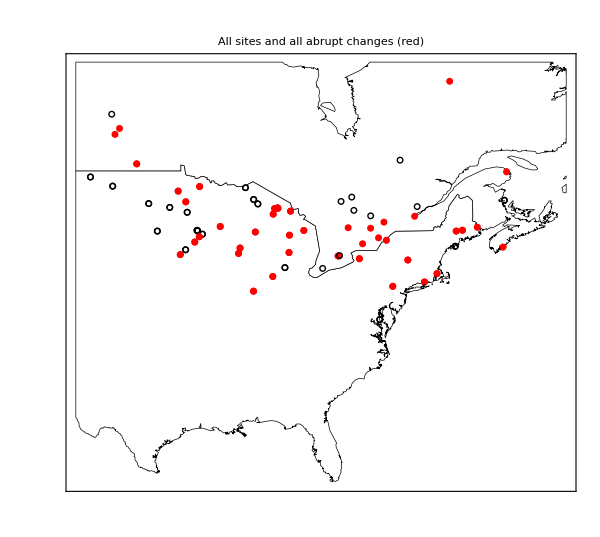

```mathematica
pt = {Graphics[{EdgeForm[{AbsoluteThickness[1], Black}],FaceForm[None],Disk[{0,0},0.1]}],Graphics[{EdgeForm[{AbsoluteThickness[1], Red}],FaceForm[Red,Opacity[0.9]],Disk[{0,0},0.1]}]};
SeedRandom[1];
sda = DA[Select[#"num_AC" > 0 &],{"lat","lon","num_AC"}];
allp = Table[{GeoMarker[ Values[Normal[DA[i,{"lat","lon"}]]],If[DA[i,"num_AC"]==0,pt[[1]],pt[[2]]],"Scale"-> 0.6]},{i,Length@DA}];

gr ={{25.,55.5},{-105.,-59.}};
ffA1=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->600,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,LabelStyle->Directive[Black,12,FontFamily->"Arial"] ,PlotLabel->"All sites and all abrupt changes (red)"]
```

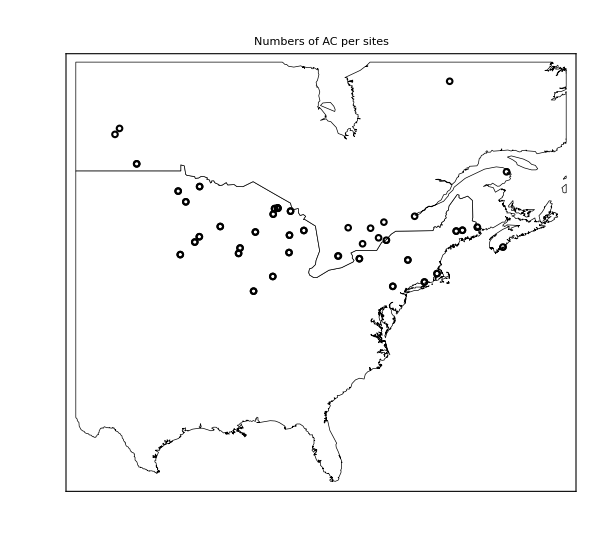

```mathematica
pt = Graphics[{EdgeForm[{AbsoluteThickness[1.5], Black}],FaceForm[None],Disk[{0,0},0.1]}];
SeedRandom[1];
sda = DA[Select[#"num_AC" > 0 &],{"lat","lon","num_AC"}];
allp = Table[{GeoMarker[ Values[Normal[sda[i,{"lat","lon"}]]],pt,"Scale"-> sda[i,"num_AC"]/3]},{i,Length@sda}];

gr ={{25.,55.5},{-105.,-59.}};
ffA2=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->600,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,LabelStyle->Directive[Black,12,FontFamily->"Arial"] ,PlotLabel->"Numbers of AC per sites"]
```

```mathematica
FF2 = Grid[{{ffA1,ffA2}}];

Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/map_AC_all.pdf", FF2]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/map_AC_all.pdf

### Per species with abundance

```mathematica
FIG = {};
Do[
pt = {Graphics[{EdgeForm[{AbsoluteThickness[1], Gray}],FaceForm[None],Disk[{0,0},0.1]}],Graphics[{EdgeForm[{AbsoluteThickness[1], Red}],FaceForm[Red,Opacity[0.9]],Disk[{0,0},0.1]}]};
SeedRandom[1];
sda = DA[Select[#[sp] ==1 &],{"lat","lon",sp<>"_AC"}];
allp = Table[{GeoMarker[ Values[Normal[sda[i,{"lat","lon"}]]],If[sda[i,sp<>"_AC"]==0,pt[[1]],pt[[2]]],"Scale"->sda[i,sp<>"_AC"]/10+0.8]},{i,Length@sda}];

gr ={{25.,55.5},{-105.,-59.}};
ffA=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->600,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,LabelStyle->Directive[Black,12,FontFamily->"Arial"] ,PlotLabel-> Style[sp,16,Bold]] ;
AppendTo[FIG,ffA];
,{sp,SP}]
```

```mathematica
FFIG = Grid[Partition[FIG,2]];
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/map_AC_species.pdf", FFIG]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/map_AC_species.pdf

### Per species with time. Fig S4

#### Abrupt increase

```mathematica
(*pt1 = Graphics[{EdgeForm[{AbsoluteThickness[1], Gray}],FaceForm[None],Disk[{0,0},0.1]}];*)
pt2 = Graphics[{EdgeForm[{AbsoluteThickness[0.5], White}],FaceForm[ GrayLevel[(8000-#)/8000],Opacity[0.9]],Disk[{0,0},0.1]}]&;
pt1 = Graphics[Inset[Style["×",16,Orange]],ImageSize->15];
tl = Style[#,15, FontFamily->"Helvetica"]&/@Subdivide[8000,1000,5];
lg = BarLegend[GrayLevel, "TickLabels"->tl,LegendLabel-> Style["YBP       ",15,FontFamily->"Helvetica"]];
is2 = 450;
```

```mathematica
FIGI = {};
Do[

SeedRandom[1];
sda = DA[Select[#[sp] ==1 &],{"datasetID","lat","lon"}];

allp = {};
Do[
coord= sda[i,{"lat","lon"}]//Normal//Values;

siteID = sda[i,"datasetID"];
timeAC = DS[sp,siteID,"AI"];

 If[MissingQ[timeAC]==True,
gm = {GeoMarker[ RandomReal[{-0.35,0.35},2] +coord,pt1 ,"Scale"->1]};
AppendTo[allp,gm],

Do[
mark = pt2[timeAC[[j]]];
gm = {GeoMarker[ RandomReal[{-0.35,0.35},2] +coord,mark ,"Scale"->1.5]};
AppendTo[allp,gm];
,{j,Length@timeAC}];
];
,{i,Length@sda}];

pl = Row[{Style[sp,Italic , 20,FontFamily->"Helvetica"], Style[" abrupt increases",20,FontFamily->"Helvetica"]}];

gr ={{25.,55.5},{-105.,-59.}};
ffA=Legended[GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is2,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,LabelStyle->ls ,PlotLabel-> pl] ,lg] ;
AppendTo[FIGI,ffA];
,{sp,SP}];
```

#### Abrupt decrease, export AI and AD

```mathematica
FIGD = {};
Do[

SeedRandom[1];
sda = DA[Select[#[sp] ==1 &],{"datasetID","lat","lon"}];

allp = {};
Do[
coord= sda[i,{"lat","lon"}]//Normal//Values;

siteID = sda[i,"datasetID"];
timeAC = DS[sp,siteID,"AD"];

 If[MissingQ[timeAC]==True,
gm = {GeoMarker[ RandomReal[{-0.35,0.35},2] +coord,pt1 ,"Scale"->1]};
AppendTo[allp,gm],

Do[
mark = pt2[timeAC[[j]]];
gm = {GeoMarker[ RandomReal[{-0.35,0.35},2] +coord,mark ,"Scale"->1.5]};
AppendTo[allp,gm];
,{j,Length@timeAC}];
];
,{i,Length@sda}];

(*allp = Table[{GeoMarker[ RandomReal[{-0.25,0.25},2] +,If[sda[i,sp<>"_AC"]==0,pt[[1]],pt[[2]]],"Scale"->sda[i,sp<>"_AC"]/10+0.8]},{i,Length@sda}];
*)

pl = Row[{Style[sp,Italic , 20,FontFamily->"Helvetica"], Style[" abrupt decreases",20,FontFamily->"Helvetica"]}];

gr ={{25.,55.5},{-105.,-59.}};
ffA=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],allp}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is2,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,LabelStyle->ls ,PlotLabel->pl];
AppendTo[FIGD,ffA];
,{sp,SP}];
```

```mathematica
FIGS4= Grid[Partition[Riffle[FIGD,FIGI],4],Spacings ->{{0,0,5,0,0,0},3}];

Export["/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/figS4.pdf", FIGS4]
```

/Users/gola/Box Sync/projects/ACES_paleo_lottery/figs/figS4.pdf

## temp

```mathematica
d1 = Table[nm-> {(DA[All,nm<>"_AI"]//Total)  ,(DA[All,nm<>"_AD"]//Total) }, {nm,SP}]//Association
```

<|Alnus→{1,0},Fagus→{15,2},Juglans→{0,2},Picea→{8,7},PinusPinus→{2,4},PinusStrobus→{4,3},Platanus→{0,1},Tilia→{0,1},Tsuga→{14,14},Ulmus→{5,15}|>

```mathematica
d1 = Table[nm-> {1+ (DA[All,nm<>"_AI"]//Total)  ,1+  (DA[All,nm<>"_AD"]//Total) }, {nm,SP}]//Association
```

<|Alnus→{2,1},Fagus→{16,3},Juglans→{1,3},Picea→{9,8},PinusPinus→{3,5},PinusStrobus→{5,4},Platanus→{1,2},Tilia→{1,2},Tsuga→{15,15},Ulmus→{6,16}|>

```mathematica
d1=Table[Callout[{1+ (DA[All,nm<>"_AI"]//Total),1+ (DA[All,nm<>"_AD"]//Total)},nm,CalloutMarker-> "CirclePoint",LabelStyle->Directive[12,Black,FontFamily->"Helvetica"],Appearance->"CurvedLeader"],{nm,SP}];
```

```mathematica
d1 = {Callout[{5,4},Style["Alnus",Italic],After,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],Callout[{20,3},Style["Fagus",Italic],Before,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],Callout[{1,1},Style["Juglans",Italic],CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],Callout[{10,11},Style["Picea",Italic],CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],Callout[{4,7},Style["Pinus Pinus",Italic],CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],Callout[{8,8},Style["Pinus Strobus",Italic],CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],Callout[{2,2},Style["Platanus",Italic],CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],Callout[{2,2},Style["Tilia",Italic],CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],Callout[{27,17},Style["Tsuga",Italic],CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"],Callout[{5,19},Style["Ulmus",Italic],Before,CalloutMarker->"CirclePoint",LabelStyle->Directive[12,GrayLevel[0],FontFamily->"Helvetica"],Appearance->"CurvedLeader"]};
```

```mathematica
tx2 ={Log@{1,2,5,10,20},{0,1,5,10,20}}//Transpose;
```

```mathematica
ip3 = {{24,10},{20,10}};
```

```mathematica
ls2 = Directive[Black,FontFamily->"Arial",16];
f1 =Labeled[ Show[ListLogLogPlot[d1],LogLogPlot[x,{x,1,25},PlotStyle->Directive[AbsoluteThickness[1],Gray]],Frame->True,ImageSize->is,FrameTicks->{{tx2,None},{tx2,None}},LabelStyle->Directive[Black,FontFamily->"Arial",16],PlotRange->All,PlotRangeClipping->False,ImagePadding->ip3,PlotLabel->Style["A)                                                               ",14]],{"Abrupt increases","Abrupt decreases"},{Bottom,Left},RotateLabel->True,LabelStyle->ls2]
```

-Graphics-Abrupt increasesAbrupt decreases

```mathematica
allAD = Table[DS[nm,All,"AD"]//DeleteMissing//Normal //Values ,{nm,SP}]//Flatten;
allAI = Table[DS[nm,All,"AI"]//DeleteMissing//Normal //Values ,{nm,SP}]//Flatten;
```

```mathematica
diffAI= Differences[Sort[allAI]];
cvAI =Round[ StandardDeviation[diffAI]/Mean[diffAI]//N,0.01];
egAI =  Text[Framed[Style["N = "<> ToString@Length@allAI <> "\n CV = " <> ToString@cvAI,12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.88}]];
gAI  = {allAI,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allAI]]}//Transpose;

diffAD= Differences[Sort[allAD]];
cvAD =Round[ StandardDeviation[diffAD]/Mean[diffAD]//N,0.01];
egAD =  Text[Framed[Style["N = "<> ToString@Length@allAD <> "\n CV = " <> ToString@cvAD,12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.88}]];
gAD  = {allAD,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allAD]]}//Transpose;
```

```mathematica
ls2 = Directive[Black,FontFamily->"Arial",16];
f2a =Labeled[ SmoothHistogram[allAI,{200,"Gaussian"},
Epilog->egAI,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gAI,None},LabelStyle->ls2,ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip3,PlotLabel->Style["B)                                                               ",14]],{"Density: abrupt increases","Years Before Present"},{Left,Bottom},RotateLabel->True,LabelStyle->ls2];
f2b = Labeled[SmoothHistogram[allAD,{200,"Gaussian"},
Epilog->egAD,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gAD,None},LabelStyle->ls2,ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip3,PlotLabel->Style["C)                                                               ",14]],{"Density: abrupt decreases","Years Before Present"},{Left,Bottom},RotateLabel->True,LabelStyle->ls2];
```

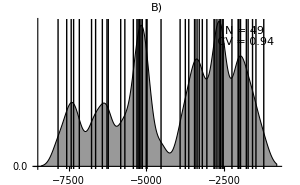
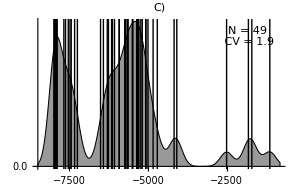
-Graphics-Abrupt increasesAbrupt decreases
-Graphics-Density: abrupt increasesYears Before Present
-Graphics-Density: abrupt decreasesYears Before Present

```mathematica
FX = Grid[{{f1,f2a,f2b}}//Transpose]
```

### Recycle if there is an need to partition the abrupt changes between 2 groups of species

```mathematica
SPd = DeleteCases[SP, "Tsuga"|"Fagus"|"Picea"];
SPi = DeleteCases[SP, "Tsuga"|"Ulmus"|"Picea"];
SPD = Complement[SP,SPD];
SPI = Complement[SP,SPI];
```

```mathematica
allAD = Table[DS[nm,All,"AD"]//DeleteMissing//Normal //Values ,{nm,SPD}]//Flatten;
allAI = Table[DS[nm,All,"AI"]//DeleteMissing//Normal //Values ,{nm,SPI}]//Flatten;
```

```mathematica
diffAI= Differences[Sort[allAI]];
cvAI =Round[ StandardDeviation[diffAI]/Mean[diffAI]//N,0.01];
egAI =  Text[Framed[Style["N = "<> ToString@Length@allAI <> "\n CV = " <> ToString@cvAI,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
gAI  = {allAI,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allAI]]}//Transpose;

diffAD= Differences[Sort[allAD]];
cvAD =Round[ StandardDeviation[diffAD]/Mean[diffAD]//N,0.01];
egAD =  Text[Framed[Style["N = "<> ToString@Length@allAD <> "\n CV = " <> ToString@cvAD,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
gAD  = {allAD,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allAD]]}//Transpose;
```

```mathematica
tx = {Automatic,{{0,"0.0"},{0.0005,"0.5"},{0.001,"1.0"},{0.0015,"1.5"},{0.003,"2.0"}}};
```

```mathematica
f2a = SmoothHistogram[allAI,{200,"Gaussian"},
Epilog->egAI,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gAI,None},LabelStyle->ls,PlotLabel-> "Abrupt increases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2];
f2b = SmoothHistogram[allAD,{200,"Gaussian"},
Epilog->egAD,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gAD,None},LabelStyle->ls,PlotLabel-> "Abrupt decreases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2];
```

```mathematica
allad = Table[DS[nm,All,"AD"]//DeleteMissing//Normal //Values ,{nm,SPd}]//Flatten;
allai = Table[DS[nm,All,"AI"]//DeleteMissing//Normal //Values ,{nm,SPi}]//Flatten;
```

```mathematica
diffai= Differences[Sort[allai]];
cvai =Round[ StandardDeviation[diffai]/Mean[diffai]//N,0.01];
egai =  Text[Framed[Style["N = "<> ToString@Length@allai <> "\n CV = " <> ToString@cvai,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
gai  = {allai,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allai]]}//Transpose;

diffad= Differences[Sort[allad]];
cvad =Round[ StandardDeviation[diffad]/Mean[diffad]//N,0.01];
egad =  Text[Framed[Style["N = "<> ToString@Length@allad <> "\n CV = " <> ToString@cvad,12,FontFamily->"Helevetica"],Background->White],Scaled[{0.85,.88}]];
gad  = {allad,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[allad]]}//Transpose;
```

```mathematica
f3a = SmoothHistogram[allai,{200,"Gaussian"},
Epilog->egai,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gai,None},LabelStyle->ls,PlotLabel-> "Abrupt increases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2];
f3b = SmoothHistogram[allad,{200,"Gaussian"},
Epilog->egad,AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,8500},{0,0.001}},AxesOrigin-> {8500,0},ScalingFunctions->sf,GridLines->{gad,None},LabelStyle->ls,PlotLabel-> "Abrupt decreases",ImageSize->is,Ticks->tx,PlotRangeClipping->False,ImagePadding->ip2];
```

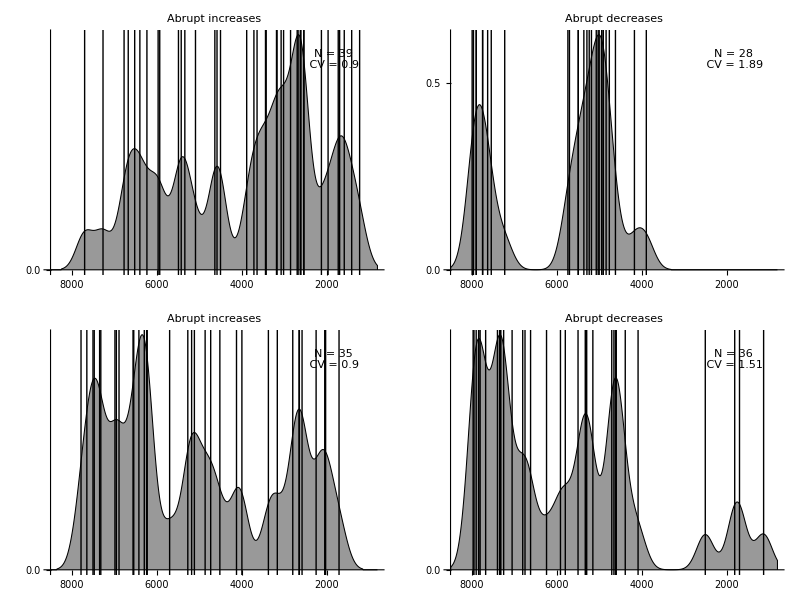

```mathematica
d2 =Grid[{{f2a,f2b},{f3a,f3b}}]
```